Your Title Here

```mathematica
(*{RGBColor[0.,0.76,0.34],PointSize[0.015],
Table[Point[{RandomReal[{0.05,0.95}],RandomReal[{0.3,0.7}]}],{xA*50}],
Table[Point[{RandomReal[{3.05,3.95}],RandomReal[{0.05,leverA-0.05}]}],{xA*50}],
Table[Point[{RandomReal[{3.05,3.95}],RandomReal[{leverA+0.05,0.95}]}],{xA*50}]
},
{Blue,PointSize[0.022],
Table[Point[{RandomReal[{1.55,2.45}],RandomReal[{0.3,0.7}]}],{xB*50}],
Table[Point[{RandomReal[{3.05,3.95}],RandomReal[{0.05,leverA-0.05}]}],{xB*50}],
Table[Point[{RandomReal[{3.05,3.95}],RandomReal[{leverA+0.05,0.95}]}],{xB*50}]
},*)
(*If[phase,{
{FaceForm[Opacity[0.3,color]],Rectangle[{3,0},{4,leverB}]},
{FaceForm[Opacity[0.3,RGBColor[0.,0.76,0.34]]],Rectangle[{3,leverB},{4,1}]}},
{FaceForm[None],Rectangle[{3,0},{4,1}]}]*)
```

```mathematica
Txy=Quiet@Interpolation[{{0.1,180},{0.15,190},{0.2,200},{0.25,208},(*{0.3,213},*){0.4,219},(*{0.5,221},*){0.55,221},(*{0.65,219},*){0.65,216},(*{0.75,209},*){0.8,180}},InterpolationOrder->5];
p1=Plot[Txy[x],{x,0.1,0.8},PlotStyle->{Thick,Black},Frame->True,FrameLabel->{Style["mole fraction A",17],Style["temperature (K)",17]},LabelStyle->{Black,13},AxesOrigin->{0,180},PlotRange->{{0,1},{180,260}},PlotRangeClipping->False];
```

```mathematica
Manipulate[
Module[{T,z,phase,xB,xA,leverB,n,color,visual},
T=comp[[2]];
z=comp[[1]];
(*T=200;z=0.3;*)
phase=Quiet[T≤Txy[z]];
xB=If[phase,x/.Quiet@FindRoot[T==Txy[x],{x,0.1}],1-z];
xA=If[phase,x/.Quiet@FindRoot[T==Txy[x],{x,1}],z];
(*leverA=If[xB≤z≤xA,(z-xB)/(xA-xB),0];*)
leverB=If[phase,(z-xA)/(xB-xA),1];
n=50;
color=Blue;
visual=Graphics[{
{RGBColor[0.,0.76,0.34],PointSize[0.015],
Table[{
Point[{RandomReal[{0.05,0.95}],RandomReal[{0.3,0.7}]}],
If[phase,{
Point[{RandomReal[{3.05,3.95}],RandomReal[{0.05,leverB-0.05}]}],
Point[{RandomReal[{3.05,3.95}],RandomReal[{leverB+0.05,0.95}]}]},
Point[{RandomReal[{3.05,3.95}],RandomReal[{0.05,0.95}]}]
]},{xA*n}]},
{color,PointSize[0.022],
Table[{
Point[{RandomReal[{1.55,2.45}],RandomReal[{0.3,0.7}]}],
If[phase,{
Point[{RandomReal[{3.05,3.95}],RandomReal[{0.05,leverB-0.05}]}],
Point[{RandomReal[{3.05,3.95}],RandomReal[{leverB+0.05,0.95}]}]},
Point[{RandomReal[{3.05,3.95}],RandomReal[{0.05,0.95}]}]
]},{xB*n}]},
{EdgeForm[{Thick,Black}],FaceForm[None],Rectangle[{0,0.25},{1,0.75}],Rectangle[{1.5,0.25},{2.5,0.75}],Rectangle[{3,0},{4,1}]},
If[phase,{Thick,Line[{{3,leverB},{4,leverB}}]}],
{Thick,
Line[{{4.05,0.01},{4.1,0.01},{4.1,leverB-0.02},{4.05,leverB-0.02}}],
Line[{{4.1,0.5*leverB},{4.2,0.5*leverB}}],
If[phase,{
Line[{{4.05,leverB+0.02},{4.1,leverB+0.02},{4.1,0.99},{4.05,0.99}}],
Line[{{4.1,1-0.5*(1-leverB)},{4.2,1-0.5*(1-leverB)}}]}]
},
Text[Style["+",25],{1.25,0.5}],Text[Style["→",25],{2.75,0.5}],
Text[Style["pure A",16],{0.5,0.12}],
Text[Style["pure B",16],{2,0.12}],
Text[Style[Column[{Row[{Subscript[Style["x",Italic],"A"]," = ",NumberForm[xA,{2,2}]}],Row[{Subscript[Style["x",Italic],"B"]," = ",NumberForm[xB,{2,2}]}]}],16],{3.5,-0.12},{0,1}],
If[phase,{
Text[Style["β phase",16],{4.25,0.5*leverB},{-1,0}],
Text[Style["α phase",16],{4.25,1-0.5*(1-leverB)},{-1,0}]},
Text[Style[Column[{"vapor","phase"},Center],16],{4.35,0.5},{-1,0}]]
},ImageSize->{450,150},PlotRange->{{-0.05,4.8},{-0.5,1.05}}];

Show[p1,
Graphics[{
Text[Style["pure B",16,color],{0,172}],
Text[Style["pure A",16,RGBColor[0.,0.35,0.1]],{1,172}],
If[phase,{Thick,Dashed,color,Line[{{xB,180},{xB,T},{z,T}}],RGBColor[0.,0.76,0.34],Line[{{z,T},{xA,T},{xA,180}}]}],
Inset[visual,{0.5,240}]
}],ImageSize->550,ImagePadding->{{45,20},{40,5}}]
],
Style["move black point around diagram",Bold],
Control[{{comp,{0.3,190}},Locator,Appearance->Graphics[{Disk[]},ImageSize->10]}],
(*Control[{{nn,50,""},50,500,5,Appearance->"Labeled"}],*)SaveDefinitions->True]
```

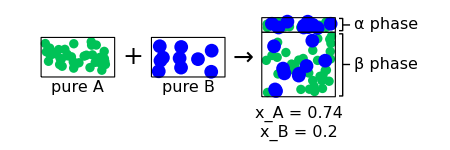

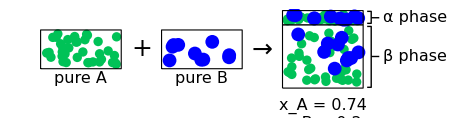
```mathematica
ImageDimensions[-Graphics-]
```

{450,148}





Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Contributed by: XXXX